```mathematica
k = 5
```

5

```mathematica
range ={-100,100}
```

{-100,100}

```mathematica
NN = RandomInteger[{10,20},k]
```

{16,13,19,18,12}

```mathematica
σ = RandomReal[{100,100}, k]
```

{100.,100.,100.,100.,100.}

```mathematica
centroids = RandomReal[range,{k,2}]
```

{{54.5701,23.8591},{71.791,35.1571},{-85.7741,-81.8626},{85.7219,87.5763},{52.0957,95.349}}

```mathematica
X =Table[
 RandomVariate[MultinormalDistribution[centroids[[i]], DiagonalMatrix[{σ[[i]],σ[[i]]}]],NN[[1]]], {i, 1, k}]
```

{{{66.1157,9.45695},{58.3728,33.5182},{52.3382,22.8731},{68.5563,24.2383},{51.3149,21.1249},{47.5206,40.1831},{67.6816,21.5564},{64.1214,36.1417},{58.3924,21.8781},{52.5652,16.7406},{47.6764,35.9867},{43.0303,40.7377},{59.5255,13.1223},{53.3674,29.8873},{63.3037,22.8668},{42.8044,34.3084}},{{82.841,43.7521},{74.1235,42.8257},{71.9416,26.4038},{85.5265,16.1288},{75.6822,41.9444},{78.6871,30.5983},{69.0748,41.8332},{56.1416,31.6766},{74.8982,30.2768},{76.8808,35.3066},{71.4197,34.8091},{59.6878,23.5268},{61.4744,41.7057},{64.3563,30.2511},{64.1371,39.1705},{81.334,38.4608}},{{-89.899,-83.416},{-77.7436,-85.3406},{-83.8259,-75.7438},{-91.1384,-76.4979},{-83.2622,-77.947},{-89.1586,-73.4724},{-91.8948,-82.4711},{-93.16,-84.3018},{-73.3845,-99.3086},{-80.7764,-93.3068},{-90.4203,-84.2158},{-86.241,-71.7137},{-82.1896,-102.202},{-77.2034,-89.8875},{-80.2626,-92.8421},{-85.7963,-78.8857}},{{78.8126,75.1513},{71.068,86.3514},{74.9941,92.0946},{80.5274,75.1631},{85.7271,70.8705},{87.5452,98.3483},{86.9873,83.7509},{79.5255,84.2888},{84.1937,80.0841},{99.6947,76.6155},{96.1617,95.8425},{98.6195,94.6341},{100.987,102.565},{92.3081,90.0245},{96.4214,89.6405},{88.9677,95.2112}},{{42.2128,86.3063},{49.8599,97.0847},{62.2002,99.482},{37.999,86.2593},{55.8773,96.4522},{55.1521,84.179},{63.9855,93.9114},{50.5292,110.443},{54.1684,102.098},{26.7837,94.397},{50.8414,90.2048},{41.7393,107.036},{58.6231,84.0621},{67.9508,95.0262},{55.9031,92.7648},{58.058,95.5503}}}

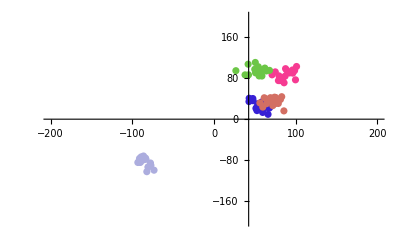

```mathematica
Show[Table[ListPlot[Style[X[[i]], RandomColor[]]],{i,1, k}], PlotRange->{2 range,2 range}]
```

```mathematica
initCentroids =  RandomReal[range,{k,2}]
```

{{90.2374,63.7269},{18.8989,71.2079},{-38.9886,-93.5874},{-63.224,92.8625},{-37.6731,83.1851}}

```mathematica
assignCluster[centroids_]:=((Position[#, Min[#]] //Flatten)[[1]]&  @ (Norm /@(centroids- ConstantArray[#, Length[centroids]])))& /@ Flatten[X, 1]
```

```mathematica
calCentroids[clusterassignment_] :=Table[Mean[Flatten[X, 1][[Position[clusterassignment,i]//Flatten]  ]],{i, 1, k}]//fillMissingCentroids
```

```mathematica
fillMissingCentroids[centroids_] := ReplacePart[centroids,Thread[#->RandomReal[range,{Length[#], 2}]]]& @ (Position[centroids,Mean[__]]//Flatten)
```

```mathematica
cluster[centroids_] := cluster[centroids, ConstantArray[{0,0}, Length[centroids]]]
```

```mathematica
cluster[centroids_, prevCentroids_] :=centroids /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] ≤1
```

```mathematica
cluster[centroids_, prevCentroids_] :=cluster[calCentroids[assignCluster[centroids]], centroids]  /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] >1
```

```mathematica
clusters =cluster[initCentroids]
```

{{87.6588,86.9148},{51.9927,94.7036},{-84.7723,-84.4721},{56.2639,26.3296},{73.7245,35.6684}}

```mathematica
clusterAssignment =assignCluster[clusters]
```

{4,4,4,4,4,4,4,5,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,4,5,5,5,4,5,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

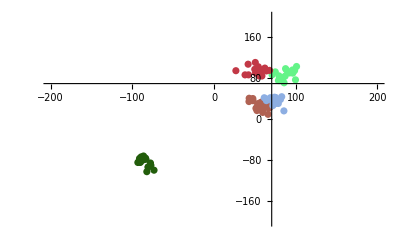

```mathematica
Show[Table[ListPlot[Style[ Flatten[X,1][[Position[clusterAssignment, i]//Flatten]], RandomColor[]]],{i,1,k}],PlotRange->{2 range,2 range}]
```

```mathematica
FindClusters[Flatten[X,1], k]
```

{{{66.1157,9.45695},{58.3728,33.5182},{52.3382,22.8731},{68.5563,24.2383},{51.3149,21.1249},{47.5206,40.1831},{67.6816,21.5564},{64.1214,36.1417},{58.3924,21.8781},{52.5652,16.7406},{47.6764,35.9867},{43.0303,40.7377},{59.5255,13.1223},{53.3674,29.8873},{63.3037,22.8668},{42.8044,34.3084},{82.841,43.7521},{74.1235,42.8257},{71.9416,26.4038},{85.5265,16.1288},{75.6822,41.9444},{78.6871,30.5983},{69.0748,41.8332},{56.1416,31.6766},{74.8982,30.2768},{76.8808,35.3066},{71.4197,34.8091},{59.6878,23.5268},{61.4744,41.7057},{64.3563,30.2511},{64.1371,39.1705},{81.334,38.4608}},{{-89.899,-83.416},{-83.8259,-75.7438},{-91.1384,-76.4979},{-83.2622,-77.947},{-89.1586,-73.4724},{-91.8948,-82.4711},{-93.16,-84.3018},{-90.4203,-84.2158},{-86.241,-71.7137},{-85.7963,-78.8857}},{{-77.7436,-85.3406},{-73.3845,-99.3086},{-80.7764,-93.3068},{-82.1896,-102.202},{-77.2034,-89.8875},{-80.2626,-92.8421}},{{78.8126,75.1513},{71.068,86.3514},{74.9941,92.0946},{80.5274,75.1631},{85.7271,70.8705},{87.5452,98.3483},{86.9873,83.7509},{79.5255,84.2888},{84.1937,80.0841},{99.6947,76.6155},{96.1617,95.8425},{98.6195,94.6341},{100.987,102.565},{92.3081,90.0245},{96.4214,89.6405},{88.9677,95.2112}},{{42.2128,86.3063},{49.8599,97.0847},{62.2002,99.482},{37.999,86.2593},{55.8773,96.4522},{55.1521,84.179},{63.9855,93.9114},{50.5292,110.443},{54.1684,102.098},{26.7837,94.397},{50.8414,90.2048},{41.7393,107.036},{58.6231,84.0621},{67.9508,95.0262},{55.9031,92.7648},{58.058,95.5503}}}

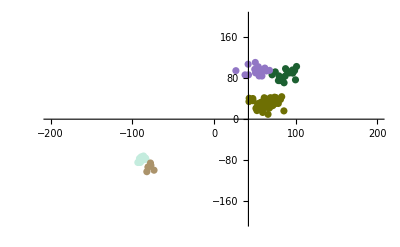

```mathematica
Show[Table[ListPlot[Style[ %[[i]], RandomColor[]]],{i,1,Length[%]}],PlotRange->{2 range,2 range}]
```